## Probability of single and double resistance for the LG model with constant birth and death rates

### Input

```mathematica
ClearAll["Global`*"]
```

```mathematica
rS=1.0;
rA=1.1;
rB=1.2;
rD=1.3;
dS=0.1;
dA=0.1;
dB=0.1;
dD=0.1;
μA= 1.0 10^-5;
μB= 1.0 10^-5;
n0 = 10^4;
kS=1.0 10^6;
kA= 1.1 10^6;
kB= 1.2 10^6;
kD= 1.3 10^6;
```

### Mean values & P_ext

```mathematica
nS[t_]:=kS/(1+(kS/n0-1)Exp[-rS(1-μA-μB) t]);Pext[t_,T_,ki_,dib_,rib_]:=(dib/ki((T-t)-(ki-1)/rib(Exp[-rib(T-t)]-1)))/(dib/ki((T-t)-(ki-1)/rib(Exp[-rib(T-t)]-1))+1);(*b is for bar*)
nAsol=NDSolve[{n'[t]==(dS+rS(1-nS[t]/kS))μA nS[t]+rA(1-μB)(1-n[t]/kA)n[t],n[0]==0},n,{t,0,tmax}];
{nA}=nAsol[[1,All,2]];
nBsol=NDSolve[{n'[t]==(dS+rS(1-nS[t]/kS))μB nS[t]+rB(1-μA)(1-n[t]/kB)n[t],n[0]==0},n,{t,0,tmax}];
{nB}=nBsol[[1,All,2]];
```

### Single resistance

```mathematica
WAB[t_,μi_]:=(dS+rS(1-nS[t]/kS))μi nS[t];
PhiA[T_]:=NIntegrate[WAB[t,μA](Pext[t,T,kA,dA(1-μB),rA(1-μB)]-1),{t,0,T}];
PhiB[T_]:=NIntegrate[WAB[t,μB](Pext[t,T,kB,dB(1-μA),rB(1-μA)]-1),{t,0,T}];
PRSingle[T_]:=1-Exp[PhiA[T]+PhiB[T]];
```

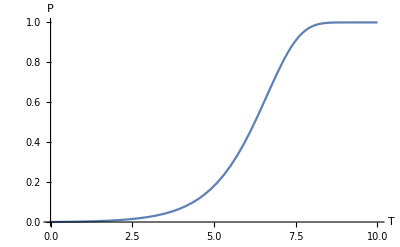

```mathematica
Plot[PRSingle[T],{T,0,10},AxesLabel->{T,P}]
```

### Double resistance

```mathematica
WD[t_]:=(dA + rA(1-nA[t]/kA))μB nA[t] + (dB + rB(1-nB[t]/kB))μA nB[t];
PhiD[T_]:=NIntegrate[WD[t](Pext[t,T,kD,dD,rD]-1),{t,0,T}];
PRDouble[T_]:=1-Exp[PhiD[T]];
```

```mathematica
Plot[PRDouble[T],{T,0,10},AxesLabel->{T,P}]
```

-Graphics-

## Probability of single and double resistance for the LG model with time-dependent birth and death rates

### Input

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

#### Constant rates

```mathematica
ρS[t_]:=0.9;
ρA[t_]:=1.0;
ρB[t_]:=1.1;
ρD[t_]:=1.2;
dS[t_]:=0.1;
dA[t_]:=0.1;
dB[t_]:=0.1;
dD[t_]:=0.1;
μA= 1.0 10^-4;
μB= 1.0 10^-4;
n0 = 5 10^5;
kS=1.0 10^6;
kA= 1.0 10^6;
kB= 1.0 10^6;
kD= 1.3 10^6;
tmax=500;
```

#### Sinusoidal rates

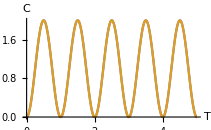

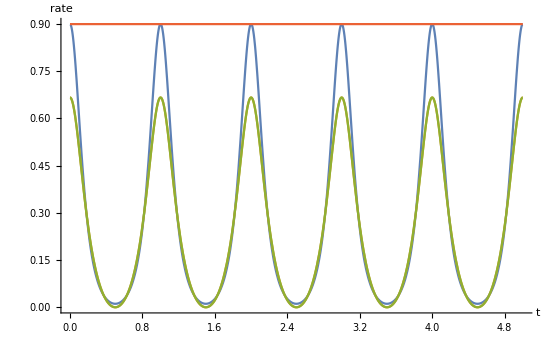

```mathematica
P=1;ΔtA = 0; ΔtB=0.0;
CA[t_]:=Piecewise[{{0,t≤ΔtA},{ Cos[(2Pi (t+P/2-ΔtA))/P]+1,t>ΔtA}}]; 
CB[t_]:=Piecewise[{{0,t≤ΔtB},{Cos[(2Pi (t+P/2-ΔtB))/P]+1,t>ΔtB}}];
fA[t_]:=1/(1+CA[t]);fB[t_]:=1/(1+CB[t]);
μA= 1 10^-5;
μB= 1 10^-6;
dS[t_]:=0.1;dA[t_]:=(1-μB)/3; dB[t_]:=(1-μA)/3;
rS[t_]:=fA[t]fB[t]-dS[t]/(1-μA-μB); 
rA[t_]:=fB[t]-dA[t]/(1-μB); 
rB[t_]:=fA[t]-dB[t]/(1-μA);
rD[t_]:=1-dD[t]; 
(*this choice of dA and dB ensures that rA and rB touch 0*)
dD[t_]:=0.1; 
n0 = 10^4;
tmax=100;
kS=1.0 10^7;
kA= 1.1 10^7;
kB= 1.2 10^7;
kD= 1.3 10^7;
Plot[{CA[t],CB[t]},{t,0,5},AxesLabel->{"T","C"}]
Plot[{rS[t],rA[t],rB[t],rD[t]},{t,0,5},PlotRange->All,AxesLabel->{"t","rate"}]
```

#### Pulsing rates

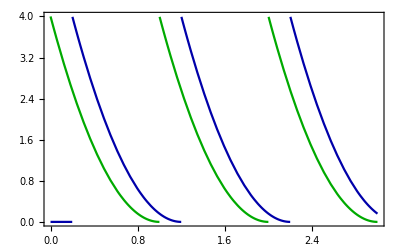

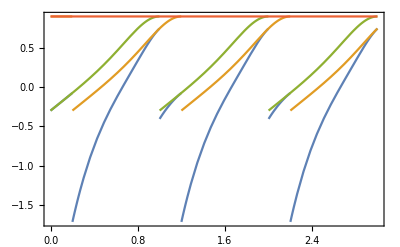

```mathematica
P=1;I0 = 0; I1 = 4.0;ΔtA=0.0; ΔtB = 0.2;
CA0[t_]:=(I1-I0)/P^2(t-ΔtA-P)^2+I0; CA[t_]:=Piecewise[{{0,t≤ΔtA},{ CA0[Mod[t-ΔtA,P]+ΔtA],t>ΔtA}}]; 
CB0[t_]:=(I1-I0)/P^2(t-ΔtB-P)^2+I0; CB[t_]:=Piecewise[{{0,t≤ΔtB},{ CB0[Mod[t-ΔtB,P]+ΔtB],t>ΔtB}}]; 
fA[t_]:=1+CA[t];fB[t_]:=1+CB[t];
dS[t_]:=0.1fA[t]fB[t];
dA[t_]:=0.1fB[t]; 
dB[t_]:=0.1fA[t];
dD[t_]:=0.1; 
ρS[t_]:=1.0/(fA[t]fB[t])-dS[t]; 
ρA[t_]:=1.0/fB[t]-dA[t];
ρB[t_]:=1.0/fA[t]-dB[t];
ρD[t_]:=0.9;
μA= 1 10^-3;
μB= 1 10^-3;
n0 = 10^4;
tmax=100;
kS=1.0 10^5;
kA= 1.1 10^5;
kB= 1.2 10^5;
kD= 1.3 10^5;
Plot[{CA[t],CB[t]},{t,0,3}, PlotStyle->{Darker[Green],Darker[Blue]},BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["C \\text{(a.u.)}",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["C_A", Magnification->1.2],MaTeX["C_B", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.88,0.79}]]
Plot[{ρS[t],ρA[t],ρB[t],ρD[t]},{t,0,3}, BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["\\text{growth rates}", Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["r_S", Magnification->1.2],MaTeX["r_A", Magnification->1.2],MaTeX["r_B", Magnification->1.2],MaTeX["r_D", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.89,0.61}]]
```

### Mean values

```mathematica
nsol=NDSolve[{nSe'[t]==ρS[t](1-μA-μB)nSe[t](1-nSe[t]/kS),nAe'[t]==(dS[t]+ρS[t](1-nSe[t]/kS))μA nSe[t]+ρA[t](1-μB)(1-nAe[t]/kA)nAe[t],nBe'[t]==(dS[t]+ρS[t](1-nSe[t]/kS))μB nSe[t]+ρB[t](1-μA)(1-nBe[t]/kB)nBe[t],nDe'[t]==(dA[t]+ρA[t](1-nAe[t]/kA))μB nAe[t]+(dB[t]+ρB[t](1-nBe[t]/kB))μA nBe[t]+ρD[t] (1-nDe[t]/kD)nDe[t],nSe[0]==n0,nAe[0]==0,nBe[0]==0,nDe[0]==0},{nSe,nAe,nBe,nDe},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
{nS, nA,nB,nD}=nsol[[1,All,2]];
nT[t_]:=nS[t] + nA[t] + nB[t] + nD[t];
```

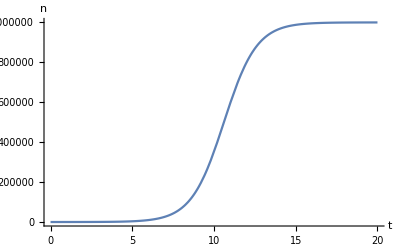

```mathematica
Plot[{nA[t]},{t,0,20},PlotRange->All,AxesLabel->{"t","n"}]
```

### P_ext

```mathematica
nsolext=NDSolve[{nAe'[t]==ρA[t](1-μB)(1-nAe[t]/kA)nAe[t],nBe'[t]==ρB[t](1-μA)(1-nBe[t]/kB)nBe[t],nDe'[t]==ρD[t] (1-nDe[t]/kD)nDe[t],nAe[0]==1,nBe[0]==1,nDe[0]==1},{nAe,nBe,nDe},{t,0,tmax}];
{nA0,nB0,nD0}=nsolext[[1,All,2]];
```

```mathematica
nAp[t_ ?NumericQ,tp_ ?NumericQ]:=(kA(kA/nA0[t]-1))/((kA-1)(kA/nA0[tp]-1)+(kA/nA0[t]-1));nBp[t_ ?NumericQ,tp_ ?NumericQ]:=(kB(kB/nB0[t]-1))/((kB-1)(kB/nB0[tp]-1)+(kB/nB0[t]-1));
nDp[t_ ?NumericQ,tp_ ?NumericQ]:=(kD(kD/nD0[t]-1))/((kD-1)(kD/nD0[tp]-1)+(kD/nD0[t]-1));
```

```mathematica
PeFA[t_?NumericQ,T_?NumericQ] := NIntegrate[(dA[tp] (1-μB))/nAp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFB[t_?NumericQ,T_?NumericQ] := NIntegrate[(dB[tp] (1-μA))/nBp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFD[t_?NumericQ,T_?NumericQ] := NIntegrate[dD[tp]/nDp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

```mathematica
PextA[t_,T_]:=PeFA[t,T]/(1 + PeFA[t,T]);PextB[t_,T_]:=PeFB[t,T]/(1 + PeFB[t,T]);PextD[t_,T_]:=PeFD[t,T]/(1 + PeFD[t,T]);
```

### Single resistance

```mathematica
WA[t_]:=nS[t](dS[t]+ρS[t](1-nS[t]/kS))μA;
WB[t_]:=nS[t](dS[t]+ρS[t](1-nS[t]/kS))μB;
PRSingle[T_]:=1-Exp[NIntegrate[WA[t](PextA[t,T] - 1) + WB[t](PextB[t,T] - 1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->2]];
```

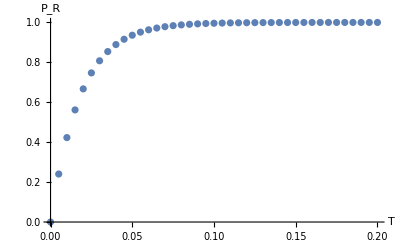

```mathematica
ListPlot[Table[{T,PRSingle[T]},{T,0,0.2,0.005}],AxesLabel->{"T","P_R"}]
```

### Double resistance

```mathematica
Clear[PRDouble]
```

```mathematica
WD[t_]:=(dA[t] + ρA[t](1-nA[t]/kA))μB nA[t] + (dB[t] + ρB[t](1-nB[t]/kB))μA nB[t];
PhiD[T_]:=NIntegrate[WD[t](PextD[t,T]-1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PRDouble[T_]:=PRDouble[T]=1-Exp[PhiD[T]];
```

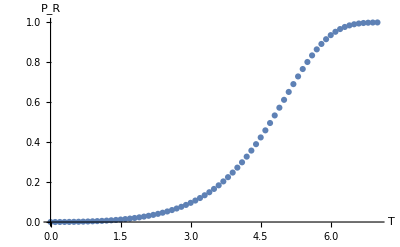

```mathematica
ListPlot[Table[{T,PRDouble[T]},{T,0,7,.1}],PlotRange->All,AxesLabel->{"T","P_R"}]
```